```mathematica
Clear["Global`*"]
```

```mathematica
Computing the orbitals
```

```mathematica
COEFF1s={c1->0.9358190,c2->0.0652831,c3->0.0004788,c4->-0.0005269,c5->0.0075836,c6->0.0020628};
COEFF2s={c1->-0.2070314,c2->-0.0106959,c3->0.4706099,c4->0.5355402,c5->-0.1035593,c6->0.1263419};
COEFF2p={c1->0.4487862,c2->0.4485854,c3->0.1654066,c4->0.0084335};
EXPs={e1->-5.450236,e2->-9.584061,e3->-1.304429,e4->-1.899079,e5->-3.753271,e6->-3.753486};
EXPp={e1->-1.058381,e2->-1.648879,e3->-2.808762,e4->-6.781327};
Ns={n1->1,n2->1,n3->2,n4->2,n5->2,n6->3};
Np={n1->2,n2->2,n3->2,n4->2};
Occupations={n1sα->1,n1sβ->1,n2sα->1,n2sβ->1,n2p0α->1,n2p0β->0,n2p1α->1,n2p1β->0,n2pm1α->0,n2pm1β->0};
Nelα:=(n1sα+n2sα+n2p0α+n2p1α+n2pm1α)/.Occupations;
Nelβ:=(n1sβ+n2sβ+n2p0β+n2p1β+n2pm1β)/.Occupations;
Nel:=Nelα+Nelβ
```

```mathematica
Nrmlz[ea_,na_]:=(-2*ea)^(na+.5)/(√((2*na)!))
NrmS={Nrm1->Nrmlz[e1,n1],Nrm2->Nrmlz[e2,n2],Nrm3->Nrmlz[e3,n3],Nrm4->Nrmlz[e4,n4],Nrm5->Nrmlz[e5,n5],Nrm6->Nrmlz[e6,n6]}/.Union[EXPs,Ns]
NrmP={Nrm1->Nrmlz[e1,n1],Nrm2->Nrmlz[e2,n2],Nrm3->Nrmlz[e3,n3],Nrm4->Nrmlz[e4,n4]}/.Union[EXPp,Np]
```

{Nrm1→25.448,Nrm2→59.3409,Nrm3→2.24399,Nrm4→5.73888,Nrm5→31.5133,Nrm6→43.1977}

{Nrm1→1.33068,Nrm2→4.03126,Nrm3→15.2671,Nrm4→138.279}

```mathematica
ϕ1s[r_]:=((c1*Nrm1*r^(n1-1)*ⅇ^(e1*r)+c2*Nrm2*r^(n2-1)*ⅇ^(e2*r)+c3*Nrm3*r^(n3-1)*ⅇ^(e3*r)+c4*Nrm4*r^(n4-1)*ⅇ^(e4*r)+c5*Nrm5*r^(n5-1)*ⅇ^(e5*r)+c6*Nrm6*r^(n6-1)*ⅇ^(e6*r))*√(1/(4*Pi))/.Union[COEFF1s,EXPs,Ns,NrmS])
ϕ2s[r_]:=((c1*Nrm1*r^(n1-1)*ⅇ^(e1*r)+c2*Nrm2*r^(n2-1)*ⅇ^(e2*r)+c3*Nrm3*r^(n3-1)*ⅇ^(e3*r)+c4*Nrm4*r^(n4-1)*ⅇ^(e4*r)+c5*Nrm5*r^(n5-1)*ⅇ^(e5*r)+c6*Nrm6*r^(n6-1)*ⅇ^(e6*r))*√(1/(4*Pi))/.Union[COEFF2s,EXPs,Ns,NrmS])
ϕ2pR[r_]:=((c1*Nrm1*r^(n1-1)*ⅇ^(e1*r)+c2*Nrm2*r^(n2-1)*ⅇ^(e2*r)+c3*Nrm3*r^(n3-1)*ⅇ^(e3*r)+c4*Nrm4*r^(n4-1)*ⅇ^(e4*r))*√(1/(4*Pi))/.Union[COEFF2p,EXPp,Np,NrmP])
ϕ2p0θ[θ_]:=√3*Cos[θ]
ϕ2p1θ[θ_]:=√(3/2)*Sin[θ]
ϕ2p0[r_,θ_]:=ϕ2pR[r]*ϕ2p0θ[θ]
ϕ2p1[r_,θ_]:=ϕ2pR[r]*ϕ2p1θ[θ]
```

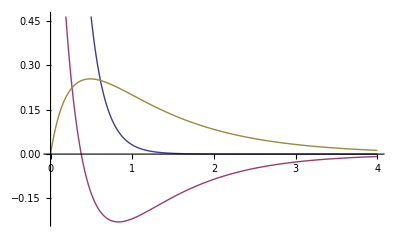

```mathematica
Plot[{ϕ1s[r],-ϕ2s[r],ϕ2pR[r]},{r,0,4}]
```

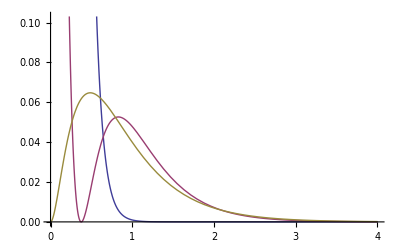

```mathematica
Plot[{ϕ1s[r]^2,ϕ2s[r]^2,ϕ2pR[r]^2},{r,0,4}]
```

```mathematica
NIntegrate[ϕ1s[r]^2*(4*Pi*r^2),{r,0,Infinity},AccuracyGoal->8]
```

1.

```mathematica
NIntegrate[ϕ2s[r]^2*(4*Pi*r^2),{r,0,Infinity},AccuracyGoal->8]
```

1.

```mathematica
NIntegrate[ϕ2p0[r,θ]^2*(2*Pi*r^2*Sin[θ]),{θ,0,π},{r,0,Infinity},AccuracyGoal->8]
```

1.

```mathematica
NIntegrate[ϕ2p1[r,θ]^2*(2*Pi*r^2*Sin[θ]),{θ,0,π},{r,0,Infinity},AccuracyGoal->8]
```

1.

```mathematica
Derivative of the orbitals
```

```mathematica
Drϕ1s[r_]:=((c1*Nrm1*((n1-1)/r+e1)*r^(n1-1)*ⅇ^(e1*r)+c2*Nrm2*((n2-1)/r+e2)*r^(n2-1)*ⅇ^(e2*r)+c3*Nrm3*((n3-1)/r+e3)*r^(n3-1)*ⅇ^(e3*r)+c4*Nrm4*((n4-1)/r+e4)*r^(n4-1)*ⅇ^(e4*r)+c5*Nrm5*((n5-1)/r+e5)*r^(n5-1)*ⅇ^(e5*r)+c6*Nrm6*((n6-1)/r+e6)*r^(n6-1)*ⅇ^(e6*r))*√(1/(4*Pi))/.Union[COEFF1s,EXPs,Ns,NrmS])
Drϕ2s[r_]:=((c1*Nrm1*((n1-1)/r+e1)*r^(n1-1)*ⅇ^(e1*r)+c2*Nrm2*((n2-1)/r+e2)*r^(n2-1)*ⅇ^(e2*r)+c3*Nrm3*((n3-1)/r+e3)*r^(n3-1)*ⅇ^(e3*r)+c4*Nrm4*((n4-1)/r+e4)*r^(n4-1)*ⅇ^(e4*r)+c5*Nrm5*((n5-1)/r+e5)*r^(n5-1)*ⅇ^(e5*r)+c6*Nrm6*((n6-1)/r+e6)*r^(n6-1)*ⅇ^(e6*r))*√(1/(4*Pi))/.Union[COEFF2s,EXPs,Ns,NrmS])
Drϕ2pR[r_]:=((c1*Nrm1*((n1-1)/r+e1)*r^(n1-1)*ⅇ^(e1*r)+c2*Nrm2*((n2-1)/r+e2)*r^(n2-1)*ⅇ^(e2*r)+c3*Nrm3*((n3-1)/r+e3)*r^(n3-1)*ⅇ^(e3*r)+c4*Nrm4*((n4-1)/r+e4)*r^(n4-1)*ⅇ^(e4*r))*√(1/(4*Pi))/.Union[COEFF2p,EXPp,Np,NrmP])
Dθϕ2p0θ[θ_]:=-√3*Sin[θ]
Dθϕ2p1θ[θ_]:=√(3/2)*Cos[θ]
```

```mathematica
Defining the density
```

```mathematica
ρα[r_,θ_]:=(n1sα*ϕ1s[r]^2+n2sα*ϕ2s[r]^2+n2p0α*ϕ2p0[r,θ]^2+(n2p1α+n2pm1α)*ϕ2p1[r,θ]^2)/.Occupations
ρβ[r_,θ_]:=(n1sβ*ϕ1s[r]^2+n2sβ*ϕ2s[r]^2+n2p0β*ϕ2p0[r,θ]^2+(n2p1β+n2pm1β)*ϕ2p1[r,θ]^2)/.Occupations
ρ[r_,θ_]:=ρα[r,θ]+ρβ[r,θ]
```

```mathematica
2*π*NIntegrate[ρβ[r,θ]*r^2*Sin[θ],{θ,0,π},{r,0,∞}]
```

2.

```mathematica
2*π*NIntegrate[ρα[r,θ]*r^2*Sin[θ],{θ,0,π},{r,0,∞}]
```

4.

```mathematica
2*π*NIntegrate[ρ[r,θ]*r^2*Sin[θ],{θ,0,π},{r,0,∞}]
```

6.

```mathematica
Defining the Desity matrices
```

```mathematica
γαα[r1_,θ1_,r2_,θ2_]:=(n1sα*ϕ1s[r1]ϕ1s[r2]+n2sα*ϕ2s[r1] ϕ2s[r2]+n2p0α*ϕ2p0[r1,θ1]*ϕ2p0[r2,θ2]+(n2p1α+n2pm1α)*ϕ2p1[r1,θ1]*ϕ2p1[r2,θ2])/.Occupations
γββ[r1_,θ1_,r2_,θ2_]:=(n1sβ*ϕ1s[r1]ϕ1s[r2]+n2sβ*ϕ2s[r1] ϕ2s[r2]+n2p0β*ϕ2p0[r1,θ1]ϕ2p0[r2,θ2]+(n2p1β+n2pm1β)*ϕ2p1[r1,θ1]*ϕ2p1[r2,θ2])/.Occupations
γααSQ[r1_,θ1_,r2_,θ2_]:=γαα[r1,θ1,r2,θ2]^2-2*((n1sα*ϕ1s[r1]ϕ1s[r2]+n2sα*ϕ2s[r1] ϕ2s[r2])*(n2p1α+n2pm1α)*ϕ2p1[r1,θ1]*ϕ2p1[r2,θ2])/.Occupations
γββSQ[r1_,θ1_,r2_,θ2_]:=γββ[r1,θ1,r2,θ2]^2-2*((n1sβ*ϕ1s[r1]ϕ1s[r2]+n2sβ*ϕ2s[r1] ϕ2s[r2])*(n2p1β+n2pm1β)*ϕ2p1[r1,θ1]*ϕ2p1[r2,θ2])/.Occupations
γ[r1_,θ1_,r2_,θ2_]:=γαα[r1,θ1,r2,θ2]+γββ[r1,θ1,r2,θ2]
```

```mathematica
NIntegrate[γαα[r,θ,r,θ]*(2*Pi*r^2*Sin[θ]),{θ,0,π},{r,0,Infinity},AccuracyGoal->8]
```

4.

```mathematica
(2 π)^2*NIntegrate[γααSQ[r1,θ1,r2,θ2]*r1^2*Sin[θ1]*r2^2*Sin[θ2],{θ2,0,π},{θ1,0,π},{r2,0,∞},{r1,0,∞},AccuracyGoal->6]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

4.

```mathematica
NIntegrate[γββ[r,θ,r,θ]*(2*Pi*r^2*Sin[θ]),{θ,0,π},{r,0,Infinity},AccuracyGoal->8]
```

2.

```mathematica
NIntegrate[γ[r,θ,r,θ]*(2*Pi*r^2*Sin[θ]),{θ,0,π},{r,0,Infinity},AccuracyGoal->8]
```

6.

```mathematica
Defining the pair density
```

```mathematica
ρ2αα[r1_,θ1_,r2_,θ2_]:=ρα[r1,θ1]ρα[r2,θ2]-γααSQ[r1,θ1,r2,θ2]
ρ2ββ[r1_,θ1_,r2_,θ2_]:=ρβ[r1,θ1]ρβ[r2,θ2]-γββSQ[r1,θ1,r2,θ2]
ρ2αβ[r1_,θ1_,r2_,θ2_]:=ρα[r1,θ1]ρβ[r2,θ2]
ρ2βα[r1_,θ1_,r2_,θ2_]:=ρβ[r1,θ1]ρα[r2,θ2]
ρ2[r1_,θ1_,r2_,θ2_]:=ρ2αα[r1,θ1,r2,θ2]+ρ2αβ[r1,θ1,r2,θ2]+ρ2βα[r1,θ1,r2,θ2]+ρ2ββ[r1,θ1,r2,θ2]
```

```mathematica
(2 π)^2*NIntegrate[ρ2αα[r1,θ1,r2,θ2]*r1^2*Sin[θ1]*r2^2*Sin[θ2],{θ2,0,π},{θ1,0,π},{r2,0,10},{r1,0,10},AccuracyGoal->4]
```

12.

```mathematica
(2 π)^2*NIntegrate[ρ2ββ[r1,θ1,r2,θ2]*r1^2*Sin[θ1]*r2^2*Sin[θ2],{θ2,0,π},{θ1,0,π},{r2,0,10},{r1,0,10},AccuracyGoal->4]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

2.00036

```mathematica
(2 π)^2*NIntegrate[ρ2αβ[r1,θ1,r2,θ2]*r1^2*Sin[θ1]*r2^2*Sin[θ2],{θ2,0,π},{θ1,0,π},{r2,0,10},{r1,0,10},AccuracyGoal->4]
```

8.0001

```mathematica
(2 π)^2*NIntegrate[ρ2[r1,θ1,r2,θ2]*r1^2*Sin[θ1]*r2^2*Sin[θ2],{θ2,0,π},{θ1,0,π},{r2,0,10},{r1,0,10},AccuracyGoal->4]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

30.

```mathematica
Derivative of the density
```

```mathematica
Drρα[r_,θ_]:=2*(n1sα*ϕ1s[r]*Drϕ1s[r]+n2sα*ϕ2s[r]*Drϕ2s[r]+ϕ2pR[r]*Drϕ2pR[r]*(n2p0α*ϕ2p0θ[θ]^2+(n2p1α+n2pm1α)*ϕ2p1θ[θ]^2))/.Occupations
Dθρα[r_,θ_]:=2*(ϕ2pR[r]^2*(n2p0α*ϕ2p0θ[θ]*Dθϕ2p0θ[θ]+(n2p1α+n2pm1α)*ϕ2p1θ[θ]*Dθϕ2p1θ[θ]))/.Occupations
Drρβ[r_,θ_]:=2*(n1sβ*ϕ1s[r]*Drϕ1s[r]+n2sβ*ϕ2s[r]*Drϕ2s[r]+ϕ2pR[r]*Drϕ2pR[r]*(n2p0β*ϕ2p0θ[θ]^2+(n2p1β+n2pm1β)*ϕ2p1θ[θ]^2))/.Occupations
Dθρβ[r_,θ_]:=2*(ϕ2pR[r]^2*(n2p0β*ϕ2p0θ[θ]*Dθϕ2p0θ[θ]+(n2p1β+n2pm1β)*ϕ2p1θ[θ]*Dθϕ2p1θ[θ]))/.Occupations
Drρ[r_,θ_]:=Drρα[r,θ]+Drρβ[r,θ]
Dθρ[r_,θ_]:=Dθρα[r,θ]+Dθρβ[r,θ]
```

```mathematica
Derivative of Density Matrices
```

```mathematica
Drγαα[r1_,θ1_,r2_,θ2_]:=(n1sα*ϕ1s[r2]*Drϕ1s[r1]+n2sα*ϕ2s[r2]*Drϕ2s[r1]+ϕ2pR[r2]*Drϕ2pR[r1]*(n2p0α*ϕ2p0θ[θ2]*ϕ2p0θ[θ1]+(n2p1α+n2pm1α)*ϕ2p1θ[θ2]*ϕ2p1θ[θ1]))/.Occupations
Dθγαα[r1_,θ1_,r2_,θ2_]:=(ϕ2pR[r2]*ϕ2pR[r1]*(n2p0α*ϕ2p0θ[θ2]*Dθϕ2p0θ[θ1]+(n2p1α+n2pm1α)*ϕ2p1θ[θ2]*Dθϕ2p1θ[θ1]))/.Occupations
Drγββ[r1_,θ1_,r2_,θ2_]:=(n1sβ*ϕ1s[r2]*Drϕ1s[r1]+n2sβ*ϕ2s[r2]*Drϕ2s[r1]+ϕ2pR[r2]*Drϕ2pR[r1]*(n2p0β*ϕ2p0θ[θ2]*ϕ2p0θ[θ1]+(n2p1β+n2pm1β)*ϕ2p1θ[θ2]*ϕ2p1θ[θ1]))/.Occupations
Dθγββ[r1_,θ1_,r2_,θ2_]:=(ϕ2pR[r2]*ϕ2pR[r1]*(n2p0β*ϕ2p0θ[θ2]*Dθϕ2p0θ[θ1]+(n2p1β+n2pm1β)*ϕ2p1θ[θ2]*Dθϕ2p1θ[θ1]))/.Occupations
DrγααSQ[r1_,θ1_,r2_,θ2_]:=(2*(n2p1α+n2pm1α)*ϕ2p1[r1,θ1]*ϕ2p1[r2,θ2]*(n1sα*ϕ1s[r2]*Drϕ1s[r1]+n2sα*ϕ2s[r2]*Drϕ2s[r1]))+(2*(n2p1α+n2pm1α)*ϕ2pR[r2]*Drϕ2pR[r1]*ϕ2p1θ[θ1]*ϕ2p1θ[θ2]*(n1sα*ϕ1s[r1]ϕ1s[r2]+n2sα*ϕ2s[r1] ϕ2s[r2]))/.Occupations
DθγααSQ[r1_,θ1_,r2_,θ2_]:=(2*(n2p1α+n2pm1α)*ϕ2pR[r2]*ϕ2pR[r1]*ϕ2p1θ[θ2]*Dθϕ2p1θ[θ1]*(n1sα*ϕ1s[r1]ϕ1s[r2]+n2sα*ϕ2s[r1] ϕ2s[r2]))/.Occupations
DrγββSQ[r1_,θ1_,r2_,θ2_]:=(2*(n2p1β+n2pm1β)*ϕ2p1[r1,θ1]*ϕ2p1[r2,θ2]*(n1sβ*ϕ1s[r2]*Drϕ1s[r1]+n2sβ*ϕ2s[r2]*Drϕ2s[r1]))+(2*(n2p1β+n2pm1β)*ϕ2pR[r2]*Drϕ2pR[r1]*ϕ2p1θ[θ1]*ϕ2p1θ[θ2]*(n1sβ*ϕ1s[r1]ϕ1s[r2]+n2sβ*ϕ2s[r1] ϕ2s[r2]))/.Occupations
DθγββSQ[r1_,θ1_,r2_,θ2_]:=(2*(n2p1β+n2pm1β)*ϕ2pR[r2]*ϕ2pR[r1]*ϕ2p1θ[θ2]*Dθϕ2p1θ[θ1]*(n1sβ*ϕ1s[r1]ϕ1s[r2]+n2sβ*ϕ2s[r1] ϕ2s[r2]))/.Occupations
Drγ[r1_,θ1_,r2_,θ2_]:=Drγαα[r1,θ1,r2,θ2]+Drγββ[r1,θ1,r2,θ2]
Dθγ[r1_,θ1_,r2_,θ2_]:=Dθγαα[r1,θ1,r2,θ2]+Dθγββ[r1,θ1,r2,θ2]
```

```mathematica
Derivative of Pair Density
```

```mathematica
Drρ2αα[r1_,θ1_,r2_,θ2_]:=Drρα[r1,θ1]ρα[r2,θ2]-2γαα[r1,θ1,r2,θ2]*Drγαα[r1,θ1,r2,θ2]+DrγααSQ[r1,θ1,r2,θ2]
Dθρ2αα[r1_,θ1_,r2_,θ2_]:=Dθρα[r1,θ1]ρα[r2,θ2]-2γαα[r1,θ1,r2,θ2]*Dθγαα[r1,θ1,r2,θ2]+DθγααSQ[r1,θ1,r2,θ2]
Drρ2ββ[r1_,θ1_,r2_,θ2_]:=Drρβ[r1,θ1]ρβ[r2,θ2]-2γββ[r1,θ1,r2,θ2]*Drγββ[r1,θ1,r2,θ2]+DrγββSQ[r1,θ1,r2,θ2]
Dθρ2ββ[r1_,θ1_,r2_,θ2_]:=Dθρβ[r1,θ1]ρβ[r2,θ2]-2γββ[r1,θ1,r2,θ2]*Dθγββ[r1,θ1,r2,θ2]+DθγββSQ[r1,θ1,r2,θ2]
Drρ2αβ[r1_,θ1_,r2_,θ2_]:=Drρα[r1,θ1]ρβ[r2,θ2]
Dθρ2αβ[r1_,θ1_,r2_,θ2_]:=Dθρα[r1,θ1]ρβ[r2,θ2]
Drρ2βα[r1_,θ1_,r2_,θ2_]:=Drρβ[r1,θ1]ρα[r2,θ2]
Dθρ2βα[r1_,θ1_,r2_,θ2_]:=Dθρβ[r1,θ1]ρα[r2,θ2]
Dθρ2βα[r1_,θ1_,r2_,θ2_]:=Dθρβ[r1,θ1]ρα[r2,θ2]
Drρ2[r1_,θ1_,r2_,θ2_]:=Drρ2αα[r1,θ1,r2,θ2]+Drρ2αβ[r1,θ1,r2,θ2]+Drρ2βα[r1,θ1,r2,θ2]+Drρ2ββ[r1,θ1,r2,θ2]
Dθρ2[r1_,θ1_,r2_,θ2_]:=Dθρ2αα[r1,θ1,r2,θ2]+Dθρ2αβ[r1,θ1,r2,θ2]+Dθρ2βα[r1,θ1,r2,θ2]+Dθρ2ββ[r1,θ1,r2,θ2]
```

```mathematica
Weiszacker Kinetic energy Calculation
```

```mathematica
(* Kinetic Energy for density *)
TE1=2*π*NIntegrate[(((r*Drρ[r,θ])^2+Dθρ[r,θ]^2)/(8 ρ[r,θ]))Sin[θ],{θ,0,π},{r,0,∞}]
```

31.9701

```mathematica
(*Spin-Resolved Kinetic Energy for density *)
TEs1=2*π*(NIntegrate[(Drρα[r,θ]^2+(Dθρα[r,θ]/r)^2)/(8*ρα[r,θ])*r^2*Sin[θ],{θ,0,π},{r,0,∞}, AccuracyGoal->6]
+NIntegrate[(Drρβ[r,θ]^2+(Dθρβ[r,θ]/r)^2)/(8*ρβ[r,θ])*r^2*Sin[θ],{θ,0,π},{r,0,∞}, AccuracyGoal->6])
```

32.1187

```mathematica
(*Spin-Resolved Kinetic Energy for density-matrices *)
2*π*4*(NIntegrate[(Drγαα[r,θ,r,θ]^2+(Dθγαα[r,θ,r,θ]/r)^2)/(8*γαα[r,θ,r,θ])*r^2*Sin[θ],{θ,0,π},{r,0,∞}, AccuracyGoal->6]
+NIntegrate[(Drγββ[r,θ,r,θ]^2+(Dθγββ[r,θ,r,θ]/r)^2)/(8*γββ[r,θ,r,θ])*r^2*Sin[θ],{θ,0,π},{r,0,∞}, AccuracyGoal->6])
```

32.1187

```mathematica
(* Kinetic Energy for pair density *)
TE2=(2 π)^2/(Nel-1)*(NIntegrate[(Drρ2[r1,θ1,r2,θ2]^2+(Dθρ2[r1,θ1,r2,θ2]/r1)^2)/(8*ρ2[r1,θ1,r2,θ2])*r1^2*Sin[θ1]*r2^2*Sin[θ2],{θ2,0,π},{θ1,0,π},{r2,0,10},{r1,0,10},AccuracyGoal->6])
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.06692 and 0.0000163967 for the integral and error estimates.

32.1111

```mathematica
(*Spin-Resolved Kinetic Energy for pair-density*)
TEs2=(2 π)^2*((NIntegrate[((Drρ2αα[r1,θ1,r2,θ2]^2+(Dθρ2αα[r1,θ1,r2,θ2]/r1)^2)/(8*(Nelα-1)*ρ2αα[r1,θ1,r2,θ2])+(Drρ2ββ[r1,θ1,r2,θ2]^2+(Dθρ2ββ[r1,θ1,r2,θ2]/r1)^2)/(8*(Nelβ-1)*ρ2ββ[r1,θ1,r2,θ2]))*r1^2*Sin[θ1]*r2^2*Sin[θ2],{θ2,0,π},{θ1,0,π},{r2,0,10},{r1,0,10},AccuracyGoal->6]))/.Occupations
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.861521 and 7.85371×10^-6 for the integral and error estimates.

34.0115

```mathematica
The Triplet Density
```

```mathematica
γααT1[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(n1sα*ϕ1s[r3]*ϕ1s[r1]+n2sα*ϕ2s[r3]*ϕ2s[r1])*((n1sα*ϕ1s[r2]*ϕ1s[r3]+n2sα*ϕ2s[r2]*ϕ2s[r3])*((n2p1α+n2pm1α)*ϕ2p1[r1,θ1]*ϕ2p1[r2,θ2])+(n1sα*ϕ1s[r1]*ϕ1s[r2]+n2sα*ϕ2s[r1]*ϕ2s[r2])*((n2p1α+n2pm1α)*ϕ2p1[r2,θ2]*ϕ2p1[r3,θ3]))/.Occupations
γααT2[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(((n1sα)^2*ϕ1s[r1] ϕ1s[r2]^2 ϕ1s[r3]+(n2sα)^2*ϕ2s[r1] ϕ2s[r2]^2 ϕ2s[r3]+n1sα*n2sα*(ϕ1s[r1]*ϕ1s[r2]*ϕ2s[r2]*ϕ2s[r3]+ϕ1s[r2]*ϕ1s[r3]*ϕ2s[r1]*ϕ2s[r2]))*((n2p1α+n2pm1α)*ϕ2p1[r3,θ3]*ϕ2p1[r1,θ1]))/.Occupations
γααT3[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(n1sα*ϕ1s[r3]*ϕ1s[r1]+n2sα*ϕ2s[r3]*ϕ2s[r1])*(n2p1α+n2pm1α)^2*(ϕ2p1[r1,θ1]*ϕ2p1[r2,θ2]^2*ϕ2p1[r3,θ3])/.Occupations
γααT4[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(n1sα*ϕ1s[r2]*ϕ1s[r3]+n2sα*ϕ2s[r2]*ϕ2s[r3])*(n2p1α+n2pm1α)^2*(ϕ2p1[r2,θ2]*ϕ2p1[r1,θ1]^2*ϕ2p1[r3,θ3])/.Occupations
γααT5[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(n1sα*ϕ1s[r1]*ϕ1s[r2]+n2sα*ϕ2s[r1]*ϕ2s[r2])*(n2p1α+n2pm1α)^2*(ϕ2p1[r1,θ1]*ϕ2p1[r3,θ3]^2*ϕ2p1[r2,θ2])/.Occupations
γααT6[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=3((n2p1α)^2*(n2pm1α)+(n2p1α)*(n2pm1α)^2)*(ϕ2p1[r1,θ1]^2*ϕ2p1[r2,θ2]^2*ϕ2p1[r3,θ3]^2)/.Occupations
```

```mathematica
γββT1[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(n1sβ*ϕ1s[r3]*ϕ1s[r1]+n2sβ*ϕ2s[r3]*ϕ2s[r1])*((n1sβ*ϕ1s[r2]*ϕ1s[r3]+n2sβ*ϕ2s[r2]*ϕ2s[r3])*((n2p1β+n2pm1β)*ϕ2p1[r1,θ1]*ϕ2p1[r2,θ2])+(n1sβ*ϕ1s[r1]*ϕ1s[r2]+n2sβ*ϕ2s[r1]*ϕ2s[r2])*((n2p1β+n2pm1β)*ϕ2p1[r2,θ2]*ϕ2p1[r3,θ3]))/.Occupations
γββT2[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(((n1sβ)^2*ϕ1s[r1] ϕ1s[r2]^2 ϕ1s[r3]+(n2sβ)^2*ϕ2s[r1] ϕ2s[r2]^2 ϕ2s[r3]+n1sβ*n2sβ*(ϕ1s[r1]*ϕ1s[r2]*ϕ2s[r2]*ϕ2s[r3]+ϕ1s[r2]*ϕ1s[r3]*ϕ2s[r1]*ϕ2s[r2]))*((n2p1β+n2pm1β)*ϕ2p1[r3,θ3]*ϕ2p1[r1,θ1]))/.Occupations
γββT3[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(n1sβ*ϕ1s[r3]*ϕ1s[r1]+n2sβ*ϕ2s[r3]*ϕ2s[r1])*(n2p1β+n2pm1β)^2*(ϕ2p1[r1,θ1]*ϕ2p1[r2,θ2]^2*ϕ2p1[r3,θ3])/.Occupations
γββT4[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(n1sβ*ϕ1s[r2]*ϕ1s[r3]+n2sβ*ϕ2s[r2]*ϕ2s[r3])*(n2p1β+n2pm1β)^2*(ϕ2p1[r2,θ2]*ϕ2p1[r1,θ1]^2*ϕ2p1[r3,θ3])/.Occupations
γββT5[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(n1sβ*ϕ1s[r1]*ϕ1s[r2]+n2sβ*ϕ2s[r1]*ϕ2s[r2])*(n2p1β+n2pm1β)^2*(ϕ2p1[r1,θ1]*ϕ2p1[r3,θ3]^2*ϕ2p1[r2,θ2])/.Occupations
γββT6[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=3((n2p1β)^2*(n2pm1β)+(n2p1β)*(n2pm1β)^2)*(ϕ2p1[r1,θ1]^2*ϕ2p1[r2,θ2]^2*ϕ2p1[r3,θ3]^2)/.Occupations
```

```mathematica
ρ3ααα[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=ρα[r1,θ1]ρα[r2,θ2]ρα[r3,θ3]-ρα[r1,θ1]γααSQ[r2,θ2,r3,θ3]-ρα[r2,θ2]γααSQ[r1,θ1,r3,θ3]-ρα[r3,θ3]γααSQ[r1,θ1,r2,θ2]+2*(γαα[r1,θ1,r2,θ2]γαα[r1,θ1,r3,θ3]γαα[r2,θ2,r3,θ3]-γααT1[r1,r2,r3,θ1,θ2,θ3]-γααT2[r1,r2,r3,θ1,θ2,θ3]-γααT3[r1,r2,r3,θ1,θ2,θ3]-γααT4[r1,r2,r3,θ1,θ2,θ3]-γααT5[r1,r2,r3,θ1,θ2,θ3]-γααT6[r1,r2,r3,θ1,θ2,θ3])
ρ3ααβ[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=ρ2αα[r1,θ1,r2,θ2]ρβ[r3,θ3]
ρ3αβα[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=ρ2αα[r1,θ1,r3,θ3]ρβ[r2,θ2]
ρ3βαα[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=ρβ[r1,θ1]ρ2αα[r2,θ2,r3,θ3]
ρ3ββα[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=ρ2ββ[r1,θ1,r2,θ2]ρα[r3,θ3]
ρ3βαβ[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=ρ2ββ[r1,θ1,r3,θ3]ρα[r2,θ2]
ρ3αββ[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=ρα[r1,θ1]ρ2ββ[r2,θ2,r3,θ3]
ρ3βββ[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=ρβ[r1,θ1]ρβ[r2,θ2]ρβ[r3,θ3]-ρβ[r1,θ1]γββSQ[r2,θ2,r3,θ3]-ρβ[r2,θ2]γββSQ[r1,θ1,r3,θ3]-ρβ[r3,θ3]γββSQ[r1,θ1,r2,θ2]+2*(γββ[r1,θ1,r2,θ2]γββ[r1,θ1,r3,θ3]γββ[r2,θ2,r3,θ3]-γββT1[r1,r2,r3,θ1,θ2,θ3]-γββT2[r1,r2,r3,θ1,θ2,θ3]-γββT3[r1,r2,r3,θ1,θ2,θ3]-γββT4[r1,r2,r3,θ1,θ2,θ3]-γββT5[r1,r2,r3,θ1,θ2,θ3]-γββT6[r1,r2,r3,θ1,θ2,θ3])
ρ3[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=ρ3ααα[r1,θ1,r2,θ2,r3,θ3]+ρ3ααβ[r1,θ1,r2,θ2,r3,θ3]+ρ3αβα[r1,θ1,r2,θ2,r3,θ3]+ρ3βαα[r1,θ1,r2,θ2,r3,θ3]+ρ3ββα[r1,θ1,r2,θ2,r3,θ3]+ρ3βαβ[r1,θ1,r2,θ2,r3,θ3]+ρ3αββ[r1,θ1,r2,θ2,r3,θ3]+ρ3βββ[r1,θ1,r2,θ2,r3,θ3]
```

```mathematica
(2 π)^3*((NIntegrate[ρ3ααα[r1,θ1,r2,θ2,r3,θ3]*r1^2*Sin[θ1]*r2^2*Sin[θ2]*r3^2*Sin[θ3],{θ3,0,π},{θ2,0,π},{θ1,0,π},{r3,0,3,10},{r2,0,3,10},{r1,0,3,10},AccuracyGoal->4]))/.Occupations
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0967643 and 0.000234612 for the integral and error estimates.

24.0024

```mathematica
(2 π)^3*((NIntegrate[ρ3ααβ[r1,θ1,r2,θ2,r3,θ3]*r1^2*Sin[θ1]*r2^2*Sin[θ2]*r3^2*Sin[θ3],{θ3,0,π},{θ2,0,π},{θ1,0,π},{r3,0,10},{r2,0,10},{r1,0,10},AccuracyGoal->4]))/.Occupations
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0967639 and 0.000135384 for the integral and error estimates.

24.0023

```mathematica
(2 π)^3*((NIntegrate[ρ3αββ[r1,θ1,r2,θ2,r3,θ3]*r1^2*Sin[θ1]*r2^2*Sin[θ2]*r3^2*Sin[θ3],{θ3,0,π},{θ2,0,π},{θ1,0,π},{r3,0,10},{r2,0,10},{r1,0,10},AccuracyGoal->4]))/.Occupations
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

8.00112

```mathematica
(2 π)^3*((NIntegrate[ρ3βββ[r1,θ1,r2,θ2,r3,θ3]*r1^2*Sin[θ1]*r2^2*Sin[θ2]*r3^2*Sin[θ3],{θ3,0,π},{θ2,0,π},{θ1,0,π},{r3,0,10},{r2,0,10},{r1,0,10},AccuracyGoal->4]))/.Occupations
```

0.

```mathematica
(2 π)^3*((NIntegrate[ρ3[r1,θ1,r2,θ2,r3,θ3]*r1^2*Sin[θ1]*r2^2*Sin[θ2]*r3^2*Sin[θ3],{θ3,0,π},{θ2,0,π},{θ1,0,π},{r3,0,10},{r2,0,10},{r1,0,10},AccuracyGoal->4]))/.Occupations
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.483815 and 0.000794116 for the integral and error estimates.

120.011

```mathematica
Derivative of the triplet density
```

```mathematica
DrγααT1[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=((n1sα*ϕ1s[r3]*Drϕ1s[r1]+n2sα*ϕ2s[r3]*Drϕ2s[r1])*((n1sα*ϕ1s[r2]*ϕ1s[r3]+n2sα*ϕ2s[r2]*ϕ2s[r3])*((n2p1α+n2pm1α)*ϕ2p1[r1,θ1]*ϕ2p1[r2,θ2])+(n1sα*ϕ1s[r1]*ϕ1s[r2]+n2sα*ϕ2s[r1]*ϕ2s[r2])*((n2p1α+n2pm1α)*ϕ2p1[r2,θ2]*ϕ2p1[r3,θ3]))+(n1sα*ϕ1s[r3]*ϕ1s[r1]+n2sα*ϕ2s[r3]*ϕ2s[r1])*((n1sα*ϕ1s[r2]*ϕ1s[r3]+n2sα*ϕ2s[r2]*ϕ2s[r3])*((n2p1α+n2pm1α)*Drϕ2pR[r1]*ϕ2p1θ[θ1]*ϕ2p1[r2,θ2])+((n2p1α+n2pm1α)*ϕ2p1[r2,θ2]*ϕ2p1[r3,θ3])*(n1sα*Drϕ1s[r1]*ϕ1s[r2]+n2sα*Drϕ2s[r1]*ϕ2s[r2])))/.Occupations
DθγααT1[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=((n1sα*ϕ1s[r3]*ϕ1s[r1]+n2sα*ϕ2s[r3]*ϕ2s[r1])*((n1sα*ϕ1s[r2]*ϕ1s[r3]+n2sα*ϕ2s[r2]*ϕ2s[r3])*((n2p1α+n2pm1α)*ϕ2pR[r1]*Dθϕ2p1θ[θ1]*ϕ2p1[r2,θ2])))/.Occupations
DrγααT2[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=((((n1sα)^2*Drϕ1s[r1] ϕ1s[r2]^2 ϕ1s[r3]+(n2sα)^2*Drϕ2s[r1] ϕ2s[r2]^2 ϕ2s[r3]+n1sα*n2sα*(Drϕ1s[r1]*ϕ1s[r2]*ϕ2s[r2]*ϕ2s[r3]+ϕ1s[r2]*ϕ1s[r3]*Drϕ2s[r1]*ϕ2s[r2]))*((n2p1α+n2pm1α)*ϕ2p1[r3,θ3]*ϕ2p1[r1,θ1]))+(((n1sα)^2*ϕ1s[r1] ϕ1s[r2]^2 ϕ1s[r3]+(n2sα)^2*ϕ2s[r1] ϕ2s[r2]^2 ϕ2s[r3]+n1sα*n2sα*(ϕ1s[r1]*ϕ1s[r2]*ϕ2s[r2]*ϕ2s[r3]+ϕ1s[r2]*ϕ1s[r3]*ϕ2s[r1]*ϕ2s[r2]))*((n2p1α+n2pm1α)*ϕ2pR[r3]*ϕ2p1θ[θ3]*Drϕ2pR[r1]*ϕ2p1θ[θ1])))/.Occupations
DθγααT2[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=((((n1sα)^2*ϕ1s[r1] ϕ1s[r2]^2 ϕ1s[r3]+(n2sα)^2*ϕ2s[r1] ϕ2s[r2]^2 ϕ2s[r3]+n1sα*n2sα*(ϕ1s[r1]*ϕ1s[r2]*ϕ2s[r2]*ϕ2s[r3]+ϕ1s[r2]*ϕ1s[r3]*ϕ2s[r1]*ϕ2s[r2]))*((n2p1α+n2pm1α)*ϕ2pR[r3]*ϕ2p1θ[θ3]*ϕ2pR[r1]*Dθϕ2p1θ[θ1])))/.Occupations
DrγααT3[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=((n1sα*ϕ1s[r3]*Drϕ1s[r1]+n2sα*ϕ2s[r3]*Drϕ2s[r1])*(n2p1α+n2pm1α)^2*(ϕ2p1[r1,θ1]*ϕ2p1[r2,θ2]^2*ϕ2p1[r3,θ3])+(n1sα*ϕ1s[r3]*ϕ1s[r1]+n2sα*ϕ2s[r3]*ϕ2s[r1])*(n2p1α+n2pm1α)^2*(Drϕ2pR[r1]*ϕ2p1θ[θ1]*ϕ2p1[r2,θ2]^2*ϕ2p1[r3,θ3]))/.Occupations
DθγααT3[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=((n1sα*ϕ1s[r3]*ϕ1s[r1]+n2sα*ϕ2s[r3]*ϕ2s[r1])*(n2p1α+n2pm1α)^2*(ϕ2pR[r1]*Dθϕ2p1θ[θ1]*ϕ2p1[r2,θ2]^2*ϕ2p1[r3,θ3]))/.Occupations
DrγααT4[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=((n1sα*ϕ1s[r2]*ϕ1s[r3]+n2sα*ϕ2s[r2]*ϕ2s[r3])*(n2p1α+n2pm1α)^2*(ϕ2pR[r2]*ϕ2p1θ[θ2]*(2*Drϕ2pR[r1]*ϕ2pR[r1])*ϕ2p1θ[θ1]^2*ϕ2pR[r3]*ϕ2p1θ[θ3]))/.Occupations
DθγααT4[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=((n1sα*ϕ1s[r2]*ϕ1s[r3]+n2sα*ϕ2s[r2]*ϕ2s[r3])*(n2p1α+n2pm1α)^2*(ϕ2pR[r2]*ϕ2p1θ[θ2]*ϕ2pR[r1]^2*(2*Dθϕ2p1θ[θ1]*ϕ2p1θ[θ1])*ϕ2pR[r3]*ϕ2p1θ[θ3]))/.Occupations
DrγααT5[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=((n1sα*Drϕ1s[r1]*ϕ1s[r2]+n2sα*ϕ2s[r1]*Drϕ2s[r2])*(n2p1α+n2pm1α)^2*(ϕ2p1[r1,θ1]*ϕ2p1[r3,θ3]^2*ϕ2p1[r2,θ2])+(n1sα*ϕ1s[r1]*ϕ1s[r2]+n2sα*ϕ2s[r1]*ϕ2s[r2])*(n2p1α+n2pm1α)^2*(Drϕ2pR[r1]*ϕ2p1θ[θ1]*ϕ2p1[r3,θ3]^2*ϕ2p1[r2,θ2]))/.Occupations
DθγααT5[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=((n1sα*ϕ1s[r1]*ϕ1s[r2]+n2sα*ϕ2s[r1]*ϕ2s[r2])*(n2p1α+n2pm1α)^2*(ϕ2pR[r1]*Dθϕ2p1θ[θ1]*ϕ2p1[r3,θ3]^2*ϕ2p1[r2,θ2]))/.Occupations
DrγααT6[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=(3((n2p1α)^2*(n2pm1α)+(n2p1α)*(n2pm1α)^2)*((2*Drϕ2pR[r1]*ϕ2pR[r1])*ϕ2p1θ[θ1]^2*ϕ2p1[r2,θ2]^2*ϕ2p1[r3,θ3]^2))/.Occupations
DθγααT6[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=(3((n2p1α)^2*(n2pm1α)+(n2p1α)*(n2pm1α)^2)*(ϕ2pR[r1]^2*(2*Dθϕ2p1θ[θ1]*ϕ2pR[θ1])*ϕ2p1[r2,θ2]^2*ϕ2p1[r3,θ3]^2))/.Occupations
```

```mathematica
DrγββT1[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(n1sβ*ϕ1s[r3]*Drϕ1s[r1]+n2sβ*ϕ2s[r3]*Drϕ2s[r1])*((n1sβ*ϕ1s[r2]*ϕ1s[r3]+n2sβ*ϕ2s[r2]*ϕ2s[r3])*((n2p1β+n2pm1β)*ϕ2p1[r1,θ1]*ϕ2p1[r2,θ2])+(n1sβ*ϕ1s[r1]*ϕ1s[r2]+n2sβ*ϕ2s[r1]*ϕ2s[r2])*((n2p1β+n2pm1β)*ϕ2p1[r2,θ2]*ϕ2p1[r3,θ3]))+(n1sβ*ϕ1s[r3]*ϕ1s[r1]+n2sβ*ϕ2s[r3]*ϕ2s[r1])*((n1sβ*ϕ1s[r2]*ϕ1s[r3]+n2sβ*ϕ2s[r2]*ϕ2s[r3])*((n2p1β+n2pm1β)*Drϕ2pR[r1]*ϕ2p1θ[θ1]*ϕ2pR[r2]*ϕ2p1θ[θ2])+((n2p1β+n2pm1β)*ϕ2p1[r2,θ2]*ϕ2p1[r3,θ3])*(n1sβ*Drϕ1s[r1]*ϕ1s[r2]+n2sβ*Drϕ2s[r1]*ϕ2s[r2]))/.Occupations
DθγββT1[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(n1sβ*ϕ1s[r3]*ϕ1s[r1]+n2sβ*ϕ2s[r3]*ϕ2s[r1])*((n1sβ*ϕ1s[r2]*ϕ1s[r3]+n2sβ*ϕ2s[r2]*ϕ2s[r3])*((n2p1β+n2pm1β)*ϕ2pR[r1]*Dθϕ2p1θ[θ1]*ϕ2pR[r2]*ϕ2p1θ[θ2]))/.Occupations
DrγββT2[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(((n1sβ)^2*Drϕ1s[r1] ϕ1s[r2]^2 ϕ1s[r3]+(n2sβ)^2*Drϕ2s[r1] ϕ2s[r2]^2 ϕ2s[r3]+n1sβ*n2sβ*(Drϕ1s[r1]*ϕ1s[r2]*ϕ2s[r2]*ϕ2s[r3]+ϕ1s[r2]*ϕ1s[r3]*Drϕ2s[r1]*ϕ2s[r2]))*((n2p1β+n2pm1β)*ϕ2p1[r3,θ3]*ϕ2p1[r1,θ1]))+(((n1sβ)^2*ϕ1s[r1] ϕ1s[r2]^2 ϕ1s[r3]+(n2sβ)^2*ϕ2s[r1] ϕ2s[r2]^2 ϕ2s[r3]+n1sβ*n2sβ*(ϕ1s[r1]*ϕ1s[r2]*ϕ2s[r2]*ϕ2s[r3]+ϕ1s[r2]*ϕ1s[r3]*ϕ2s[r1]*ϕ2s[r2]))*((n2p1β+n2pm1β)*ϕ2pR[r3]*ϕ2p1θ[θ3]*Drϕ2pR[r1]*ϕ2p1θ[θ1]))/.Occupations
DθγββT2[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(((n1sβ)^2*ϕ1s[r1] ϕ1s[r2]^2 ϕ1s[r3]+(n2sβ)^2*ϕ2s[r1] ϕ2s[r2]^2 ϕ2s[r3]+n1sβ*n2sβ*(ϕ1s[r1]*ϕ1s[r2]*ϕ2s[r2]*ϕ2s[r3]+ϕ1s[r2]*ϕ1s[r3]*ϕ2s[r1]*ϕ2s[r2]))*((n2p1β+n2pm1β)*ϕ2pR[r3]*ϕ2p1θ[θ3]*ϕ2pR[r1]*Dθϕ2p1θ[θ1]))/.Occupations
DrγββT3[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(n1sβ*ϕ1s[r3]*Drϕ1s[r1]+n2sβ*ϕ2s[r3]*Drϕ2s[r1])*(n2p1β+n2pm1β)^2*(ϕ2p1[r1,θ1]*ϕ2p1[r2,θ2]^2*ϕ2p1[r3,θ3])+(n1sβ*ϕ1s[r3]*ϕ1s[r1]+n2sβ*ϕ2s[r3]*ϕ2s[r1])*(n2p1β+n2pm1β)^2*(Drϕ2pR[r1]*ϕ2p1θ[θ1]*ϕ2p1[r2,θ2]^2*ϕ2p1[r3,θ3])/.Occupations
DθγββT3[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(n1sβ*ϕ1s[r3]*ϕ1s[r1]+n2sβ*ϕ2s[r3]*ϕ2s[r1])*(n2p1β+n2pm1β)^2*(ϕ2pR[r1]Dθϕ2p1θ[θ1]*ϕ2p1[r2,θ2]^2*ϕ2p1[r3,θ3])/.Occupations
DrγββT4[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(n1sβ*ϕ1s[r2]*ϕ1s[r3]+n2sβ*ϕ2s[r2]*ϕ2s[r3])*(n2p1β+n2pm1β)^2*(ϕ2pR[r2]*ϕ2p1θ[θ2]*(2*Drϕ2pR[r1]*ϕ2pR[r1])*ϕ2p1θ[θ1]^2*ϕ2pR[r3]*ϕ2p1θ[θ3])/.Occupations
DθγββT4[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(n1sβ*ϕ1s[r2]*ϕ1s[r3]+n2sβ*ϕ2s[r2]*ϕ2s[r3])*(n2p1β+n2pm1β)^2*(ϕ2pR[r2]*ϕ2p1θ[θ2]*ϕ2pR[r1]^2*(2*Dθϕ2p1θ[θ1]*ϕ2p1θ[θ1])*ϕ2pR[r3]*ϕ2p1θ[θ3])/.Occupations
DrγββT5[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(n1sβ*Drϕ1s[r1]*ϕ1s[r2]+n2sβ*ϕ2s[r1]*Drϕ2s[r2])*(n2p1β+n2pm1β)^2*(ϕ2pR[r1]*ϕ2p1θ[θ1]*ϕ2pR[r3]*ϕ2p1θ[θ3]*ϕ2pR[r3]*ϕ2p1θ[θ3]*ϕ2pR[r2]*ϕ2p1θ[θ2])+(n1sβ*ϕ1s[r1]*ϕ1s[r2]+n2sβ*ϕ2s[r1]*ϕ2s[r2])*(n2p1β+n2pm1β)^2*(Drϕ2pR[r1]*ϕ2p1θ[θ1]*ϕ2p1[r3,θ3]^2*ϕ2p1[r2,θ2])/.Occupations
DθγββT5[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=(n1sβ*ϕ1s[r1]*ϕ1s[r2]+n2sβ*ϕ2s[r1]*ϕ2s[r2])*(n2p1β+n2pm1β)^2*(ϕ2pR[r1]*Dθϕ2p1θ[θ1]*ϕ2p1[r3,θ3]^2*ϕ2p1[r2,θ2])/.Occupations
DrγββT6[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=3((n2p1β)^2*(n2pm1β)+(n2p1β)*(n2pm1β)^2)*((2*Drϕ2pR[r1]*ϕ2pR[r1])*ϕ2p1θ[θ1]*ϕ2p1θ[θ1]*ϕ2p1[r2,θ2]^2*ϕ2p1[r3,θ3]^2)/.Occupations
DθγββT6[r1_,r2_,r3_,θ1_,θ2_,θ3_]:=3((n2p1β)^2*(n2pm1β)+(n2p1β)*(n2pm1β)^2)*(ϕ2pR[r1]*ϕ2pR[r1]*(2*Dθϕ2p1θ[θ1]*ϕ2pR[θ1])*ϕ2p1[r2,θ2]^2*ϕ2p1[r3,θ3]^2)/.Occupations
```

```mathematica
Drρ3ααα[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=Drρα[r1,θ1]ρα[r2,θ2]ρα[r3,θ3]-Drρα[r1,θ1]γααSQ[r2,θ2,r3,θ3]-ρα[r2,θ2]*(2*γαα[r1,θ1,r3,θ3]*Drγαα[r1,θ1,r3,θ3]-DrγααSQ[r1,θ1,r3,θ3])-ρα[r3,θ3]*(2*γαα[r1,θ1,r2,θ2]*Drγαα[r1,θ1,r2,θ2]-DrγααSQ[r1,θ1,r2,θ2])+2*(Drγαα[r1,θ1,r2,θ2]γαα[r1,θ1,r3,θ3]γαα[r2,θ2,r3,θ3]+γαα[r1,θ1,r2,θ2]Drγαα[r1,θ1,r3,θ3]γαα[r2,θ2,r3,θ3]-DrγααT1[r1,r2,r3,θ1,θ2,θ3]-DrγααT2[r1,r2,r3,θ1,θ2,θ3]-DrγααT3[r1,r2,r3,θ1,θ2,θ3]-DrγααT4[r1,r2,r3,θ1,θ2,θ3]-DrγααT5[r1,r2,r3,θ1,θ2,θ3]-DrγααT6[r1,r2,r3,θ1,θ2,θ3])
Dθρ3ααα[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=Dθρα[r1,θ1]ρα[r2,θ2]ρα[r3,θ3]-Dθρα[r1,θ1]γααSQ[r2,θ2,r3,θ3]-ρα[r2,θ2]*(2*γαα[r1,θ1,r3,θ3]*Dθγαα[r1,θ1,r3,θ3]-DθγααSQ[r1,θ1,r3,θ3])-ρα[r3,θ3]*(2*γαα[r1,θ1,r2,θ2]*Dθγαα[r1,θ1,r2,θ2]-DθγααSQ[r1,θ1,r3,θ3])+2*(Dθγαα[r1,θ1,r2,θ2]γαα[r1,θ1,r3,θ3]γαα[r2,θ2,r3,θ3]+γαα[r1,θ1,r2,θ2]Dθγαα[r1,θ1,r3,θ3]γαα[r2,θ2,r3,θ3]-DθγααT1[r1,r2,r3,θ1,θ2,θ3]-DθγααT2[r1,r2,r3,θ1,θ2,θ3]-DθγααT3[r1,r2,r3,θ1,θ2,θ3]-DθγααT4[r1,r2,r3,θ1,θ2,θ3]-DθγααT5[r1,r2,r3,θ1,θ2,θ3]-DθγααT6[r1,r2,r3,θ1,θ2,θ3])
Drρ3ααβ[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=Drρ2αα[r1,θ1,r2,θ2]ρβ[r3,θ3]
Dθρ3ααβ[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=Dθρ2αα[r1,θ1,r2,θ2]ρβ[r3,θ3]
Drρ3αβα[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=Drρ2αα[r1,θ1,r3,θ3]ρβ[r2,θ2]
Dθρ3αβα[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=Dθρ2αα[r1,θ1,r3,θ3]ρβ[r2,θ2]
Drρ3βαα[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=Drρβ[r1,θ1]ρ2αα[r2,θ2,r3,θ3]
Dθρ3βαα[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=Dθρβ[r1,θ1]ρ2αα[r2,θ2,r3,θ3]
Drρ3ββα[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=Drρ2ββ[r1,θ1,r2,θ2]ρα[r3,θ3]
Dθρ3ββα[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=Dθρ2ββ[r1,θ1,r2,θ2]ρα[r3,θ3]
Drρ3βαβ[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=Drρ2ββ[r1,θ1,r3,θ3]ρα[r2,θ2]
Dθρ3βαβ[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=Dθρ2ββ[r1,θ1,r3,θ3]ρα[r2,θ2]
Drρ3αββ[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=Drρα[r1,θ1]ρ2ββ[r2,θ2,r3,θ3]
Dθρ3αββ[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=Dθρα[r1,θ1]ρ2ββ[r2,θ2,r3,θ3]
Drρ3βββ[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=Drρβ[r1,θ1]ρβ[r2,θ2]ρβ[r3,θ3]-Drρβ[r1,θ1]γββSQ[r2,θ2,r3,θ3]-ρβ[r2,θ2]*((2*γββ[r1,θ1,r3,θ3]*Drγββ[r1,θ1,r3,θ3])-DrγββSQ[r1,θ1,r3,θ3])-ρβ[r3,θ3]*((2* γββ[r1,θ1,r2,θ2]*Drγββ[r1,θ1,r2,θ2])-DrγββSQ[r1,θ1,r2,θ2])+2*(Drγββ[r1,θ1,r2,θ2]γββ[r1,θ1,r3,θ3]γββ[r2,θ2,r3,θ3]+γββ[r1,θ1,r2,θ2]Drγββ[r1,θ1,r3,θ3]γββ[r2,θ2,r3,θ3]-DrγββT1[r1,r2,r3,θ1,θ2,θ3]-DrγββT2[r1,r2,r3,θ1,θ2,θ3]-DrγββT3[r1,r2,r3,θ1,θ2,θ3]-DrγββT4[r1,r2,r3,θ1,θ2,θ3]-DrγββT5[r1,r2,r3,θ1,θ2,θ3]-DrγββT6[r1,r2,r3,θ1,θ2,θ3])
Dθρ3βββ[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=Dθρβ[r1,θ1]ρβ[r2,θ2]ρβ[r3,θ3]-Dθρβ[r1,θ1]γββSQ[r2,θ2,r3,θ3]-ρβ[r2,θ2]*((2*γββ[r1,θ1,r3,θ3]*Dθγββ[r1,θ1,r3,θ3])-DθγββSQ[r1,θ1,r3,θ3])-ρβ[r3,θ3]*((2*γββ[r1,θ1,r2,θ2]*Dθγββ[r1,θ1,r2,θ2])-DθγββSQ[r1,θ1,r2,θ2])+2*(Dθγββ[r1,θ1,r2,θ2]γββ[r1,θ1,r3,θ3]γββ[r2,θ2,r3,θ3]+γββ[r1,θ1,r2,θ2]Dθγββ[r1,θ1,r3,θ3]γββ[r2,θ2,r3,θ3]-DθγββT1[r1,r2,r3,θ1,θ2,θ3]-DθγββT2[r1,r2,r3,θ1,θ2,θ3]-DθγββT3[r1,r2,r3,θ1,θ2,θ3]-DθγββT4[r1,r2,r3,θ1,θ2,θ3]-DθγββT5[r1,r2,r3,θ1,θ2,θ3]-DθγββT6[r1,r2,r3,θ1,θ2,θ3])
Drρ3[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=Drρ3ααα[r1,θ1,r2,θ2,r3,θ3]+Drρ3ααβ[r1,θ1,r2,θ2,r3,θ3]+Drρ3αβα[r1,θ1,r2,θ2,r3,θ3]+Drρ3βαα[r1,θ1,r2,θ2,r3,θ3]+Drρ3ββα[r1,θ1,r2,θ2,r3,θ3]+Drρ3βαβ[r1,θ1,r2,θ2,r3,θ3]+Drρ3αββ[r1,θ1,r2,θ2,r3,θ3]+Drρ3βββ[r1,θ1,r2,θ2,r3,θ3]
Dθρ3[r1_,θ1_,r2_,θ2_,r3_,θ3_]:=Dθρ3ααα[r1,θ1,r2,θ2,r3,θ3]+Dθρ3ααβ[r1,θ1,r2,θ2,r3,θ3]+Dθρ3αβα[r1,θ1,r2,θ2,r3,θ3]+Dθρ3βαα[r1,θ1,r2,θ2,r3,θ3]+Dθρ3ββα[r1,θ1,r2,θ2,r3,θ3]+Dθρ3βαβ[r1,θ1,r2,θ2,r3,θ3]+Dθρ3αββ[r1,θ1,r2,θ2,r3,θ3]+Dθρ3βββ[r1,θ1,r2,θ2,r3,θ3]
```

```mathematica
Evaluating the kinetic energy functional
```

```mathematica
(*Weizsacker Kinetic Energy for Three Electrons*)
TE3=(2 π)^3/(8*(Nel-1)*(Nel-2))*((NIntegrate[((r1*Drρ3[r1,θ1,r2,θ2,r3,θ3])^2+(Dθρ3[r1,θ1,r2,θ2,r3,θ3])^2)/ρ3[r1,θ1,r2,θ2,r3,θ3]*Sin[θ1]*r2^2*Sin[θ2]*r3^2*Sin[θ3],{θ3,0,π},{θ2,0,π},{θ1,0,π},{r3,0,10},{r2,0,10},{r1,0,10},Method->{"MonteCarlo","MaxPoints"->10^9},AccuracyGoal->5]))/.Occupations
```

3.27221×10^8

```mathematica
(*Spin-Resolved Kinetic Energy *)
Iα=(2 π)^3/(8*(Nelα-1)*(Nelα-2))*(NIntegrate[((r1*Drρ3ααα[r1,θ1,r2,θ2,r3,θ3])^2+(Dθρ3ααα[r1,θ1,r2,θ2,r3,θ3])^2)/ρ3ααα[r1,θ1,r2,θ2,r3,θ3]*Sin[θ1]*r2^2*Sin[θ2]*r3^2*Sin[θ3],{θ3,0,π},{θ2,0,π},{θ1,0,π},{r3,0,10},{r2,0,10},{r1,0,10},Method->{"MonteCarlo","MaxPoints"->10^9}])/.Occupations
```

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 4.57165×10^9 and 2.41352×10^9 for the integral and error estimates.

2.3625×10^10

```mathematica
Iβ=(2 π)^2/(8*(Nelβ-1))*NIntegrate[(Drρ2ββ[r1,θ1,r2,θ2]^2+(Dθρ2ββ[r1,θ1,r2,θ2]/r1)^2)/ρ2ββ[r1,θ1,r2,θ2] r1^2*Sin[θ1]*r2^2*Sin[θ2],{θ2,0,π},{θ1,0,π},{r2,0,10},{r1,0,10},AccuracyGoal->6]/.Occupations
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

17.5906

```mathematica
TEs3=Iα+Iβ
```

2.3625×10^10